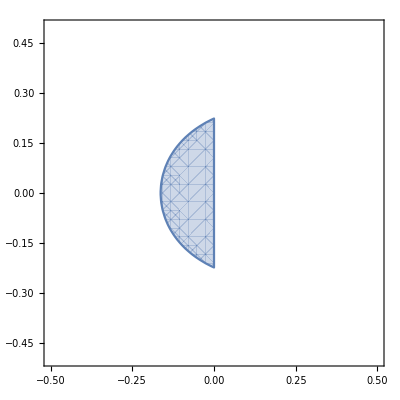

```mathematica
Clear[phi, w, sol, a, b];
w[a_, b_] := a + b*I;
phi[z_, a_, b_] := z^5 + (-1 - 1901 * w[a, b]/720) * z^4 + (2775 * w[a, b]/720) * z^3 + (-2616 * w[a, b]/720)*z^2 + (1274 * w[a, b]/720)*z + (-w[a,b]*251/720);
sol[a_, b_] := NSolve[phi[z, a, b] == 0, z];
RegionPlot[Norm[sol[a, b][[1, 1, 2]]] ≤ 1 && Norm[sol[a, b][[4, 1, 2]]] ≤ 1 && Norm[sol[a, b][[5, 1, 2]]]≤ 1,{a, -0.5, 0.5},{b, -0.5, 0.5}]
```

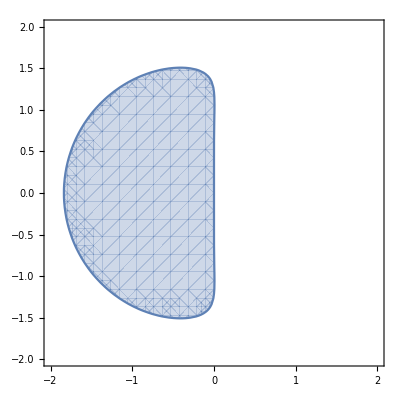

```mathematica
Clear[phi, w, sol, a, b];
w[a_, b_] := a + b*I;
phi[z_, a_, b_]:= (1 - 251*w[a, b]/720)*z^4 + (-1 - 646*w[a, b]/720)*z^3 + (264*w[a, b]/720)*z^2 + (-106 * w[a, b]/720)*z + (19*w[a, b]/720);
sol[a_, b_] := NSolve[phi[z, a, b] == 0, z];
RegionPlot[Norm[sol[a, b][[1, 1, 2]]] ≤ 1 && Norm[sol[a, b][[2, 1, 2]]] ≤ 1 && Norm[sol[a, b][[3, 1, 2]]]≤ 1 && Norm[sol[a, b][[4, 1, 2]]]≤ 1,{a, -2, 2},{b, -2, 2}]
```